### Determinant Derivation

The purpose of this notebook is to geometrically derive what a determinant is and the intuition for why it measures area (in the 2D) or volume (N-D).

-54

-54

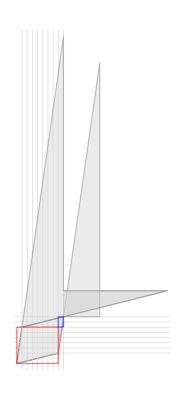

```mathematica
o= {0,0};
{a,b} ={ -1,-7};
{c,d} = {-8,-2};
v1={a,b};
v2={c,d};
Det[{v1,v2}]
a d - b c
Graphics[{
Thick,Gray,Line[{o,v1}],Line[{o,v2}],Line[{v1,v1+v2}],Line[{v2,v1+v2}],
LightGray,Opacity[0.5],Parallelogram[o,{v1,v2}],
EdgeForm[Directive[Gray,Thick]],Triangle[{o,{o⟦1⟧,Abs[(v2-v1)]⟦2⟧},{c/d*Abs[(v2-v1)]⟦2⟧,Abs[(v2-v1)]⟦2⟧}}],
Triangle[{o,{Abs[(v2-v1)]⟦1⟧,o⟦2⟧},{Abs[(v2-v1)]⟦1⟧,b/a*Abs[(v2-v1)]⟦1⟧}}],
Polygon[{{o⟦1⟧,Abs[(v2-v1)]⟦2⟧},{o⟦1⟧,Abs[(v2-v1)]⟦2⟧+b/a*Abs[(v2-v1)]⟦1⟧},v2,{c/d*Abs[(v2-v1)]⟦2⟧,Abs[(v2-v1)]⟦2⟧}}],
Red,Line[{{v1⟦1⟧,v2⟦2⟧},{v1⟦1⟧,(v1+v2)⟦2⟧}}],Line[{{(v1+v2)⟦1⟧,v2⟦2⟧},{(v1+v2)⟦1⟧,(v1+v2)⟦2⟧}}],
Line[{{v1⟦1⟧,v2⟦2⟧},{(v1+v2)⟦1⟧,v2⟦2⟧}}],Line[{{v1⟦1⟧,(v1+v2)⟦2⟧},{(v1+v2)⟦1⟧,(v1+v2)⟦2⟧}}],
Blue,Thick,Line[{o,{o⟦1⟧,v2⟦2⟧}}],Line[{{v1⟦1⟧,o⟦2⟧},{v1⟦1⟧,v2⟦2⟧}}],
Line[{o,{v1⟦1⟧,o⟦2⟧}}],Line[{{o⟦1⟧,v2⟦2⟧},{v1⟦1⟧,v2⟦2⟧}}]
},
GridLines->{Range[Min[0,a,c],Max[0,a+c],1],Range[Min[0,b,d],Max[0,b+d],1]}]
```